## Implémentation des DLL C++

## Import de la DLL

```mathematica
Clear[pathToDll]
```

```mathematica
Needs["NETLink`"];
```

```mathematica
InstallNET[];
```

```mathematica
(*pathToDll="C:\\Users\\Clem\\Documents\\ESGI\\projet_annuel_ibd3a\\C++_lib\\Dll-Machine-Learning\\x64\\Debug\\Dll-Machine-Learning.dll";*)pathToDll="D:\\git\\projet_annuel_ibd3a\\C++_lib\\Dll-Machine-Learning\\x64\\Debug\\Dll-Machine-Learning.dll";
```

```mathematica
return42ExternFunc=DefineDLLFunction["return42",pathToDll,"int",{}];
```

```mathematica
return42ExternFunc[]
```

42

## Définitions Méthodes C++

```mathematica
Clear[createLinearModelClassif, linearFitClassificationRosenblatt, linearClassify, linearCreateAndFitRegression, linearPredict, createMlp, classify, fitClassification, predict, eraseMlp];
```

Perceptron Linéaire simple

## Création/Suppression du modèle

```mathematica
createLinearModelClassif = DefineDLLFunction["createLinearModelClassif", pathToDll, "System.IntPtr", {"int", "int"}];
```

```mathematica
eraseLinearModel=DefineDLLFunction["eraseLinearModel", pathToDll, "void", {"System.IntPtr"}];
```

## Classification Linéaire Rosenblatt

### Apprentissage

```mathematica
linearFitClassificationRosenblatt = DefineDLLFunction["linearFitClassificationRosenblatt", pathToDll, "int", {"System.IntPtr", "double[]", "int", "double[]", "int", "double"}];
```

### Classify

```mathematica
linearClassify =  DefineDLLFunction["linearClassify", pathToDll, "double", {"System.IntPtr", "double[]", "int", "double[]", "int"}];
```

## Régression linéaire

### Apprentissage

```mathematica
linearCreateAndFitRegression = DefineDLLFunction["linearCreateAndFitRegression", pathToDll, "void", {"System.IntPtr", "double[]", "int", "int", "double[]","int"}];
```

### Predict

```mathematica
linearPredict = DefineDLLFunction["linearPredict", pathToDll, "void", {"System.IntPtr", "double[]", "int", "double[]", "int"}];
```

Perceptron Multi - Couches

## Création/Suppression du modèle

```mathematica
createMlp=DefineDLLFunction["createMlp",pathToDll,"System.IntPtr",{"int[]","int"}];
```

```mathematica
eraseMlp=DefineDLLFunction["eraseMlp",pathToDll,"void",{"System.IntPtr"}];
```

## Classification

### Apprentissage

```mathematica
fitClassification=DefineDLLFunction["fitClassification",pathToDll,"void",{"System.IntPtr","double[]","int","double[]"}];
```

### Classify

```mathematica
mlpClassify=DefineDLLFunction["classify",pathToDll,"void",{"System.IntPtr","double[]"}];
```

## Régression

### Apprentissage

```mathematica
fitRegression=DefineDLLFunction["fitRegression",pathToDll,"void",{"System.IntPtr","double[]","int","double[]"}];
```

### Predict

```mathematica
predict=DefineDLLFunction["predict",pathToDll,"void",{"System.IntPtr","double[]","int"}];
```

RBF Naïf

RBF

## Cas de tests

Simple Linéaire Séparable

```mathematica
Clear[a,b,c,positivePointsL, negativePointsL, f];
```

```mathematica
a = RandomInteger[{-5; 5}];
b= RandomInteger[{-5; 5}];
c= RandomInteger[{-5; 5}];
```

```mathematica
f[x_] := -a/b*x+c/b
```

```mathematica
positivePointsL = Table[x= RandomReal[{-5, 5}]; {x, f[x] + RandomReal[{0.5, 2}]}, {i,1, 3}]
```

{{-0.152063,2.57226},{0.687733,0.850224},{-0.439128,2.82445}}

```mathematica
negativePointsL = Table[x = RandomReal[{-5, 5}];
{x, f[x]-RandomReal[{0.5, 2 }]}, {i,1,3}]
```

{{-3.69358,3.26453},{-0.843826,0.243193},{3.96289,-5.87705}}

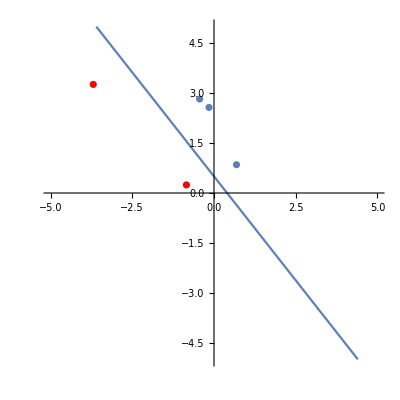

```mathematica
Show[Plot[f[x], {x,-5, 5}, PlotRange->{-5,5},
AspectRatio->1],
ListPlot[negativePointsL, PlotStyle->Red],
ListPlot[positivePointsL]]
```

Simple non linéairement séparable

```mathematica
Clear[redPointsL, bluePointsL];
```

```mathematica
redPointsL = {positivePointsL[[1]], positivePointsL[[2]], negativePointsL[[1]]}
bluePointsL = {positivePointsL[[3]], negativePointsL[[2]], negativePointsL[[3]]}
```

{{-0.152063,2.57226},{0.687733,0.850224},{-3.69358,3.26453}}

{{-0.439128,2.82445},{-0.843826,0.243193},{3.96289,-5.87705}}

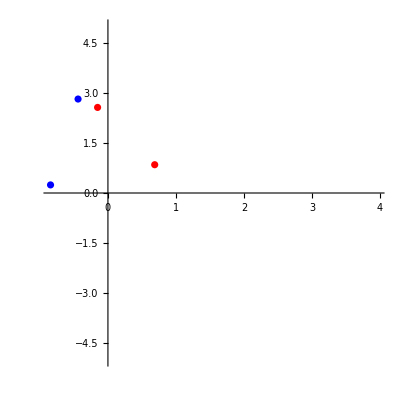

```mathematica
Show[ListPlot[bluePointsL, PlotStyle->Blue,AspectRatio->1, PlotRange->{-5, 5}], ListPlot[redPointsL, PlotStyle->Red]]
```

Cross

```mathematica
Clear[left,right,top, down];
```

```mathematica
left[x_] = (-1)*Abs[a*x];
right[x_] = Abs[a*x];
top [x_]= Abs[a];
down [x_]= (-1) * Abs[a];
```

```mathematica
rand = RandomReal[{-5,5}];
```

```mathematica
rightHighPoints = Table[x = rand;
{right[x]+RandomReal[{0.5,2}], top[x]+RandomReal[{0.5,2}]},{i,1,15}];
rightDownPoints = Table[x = rand;
{right[x]+RandomReal[{0.5,2}], down[x]-RandomReal[{0.5,2}]},{i,1,15}];
leftHighPoints = Table[x = rand;
{left[x]-RandomReal[{0.5,2}], top[x]+RandomReal[{0.5,2}]},{i,1,15}];
leftDownPoints = Table[x = RandomReal[{-5,5}];
{left[x]-RandomReal[{0.5,2}], down[x]-RandomReal[{0.5,2}]},{i,1,15}];
```

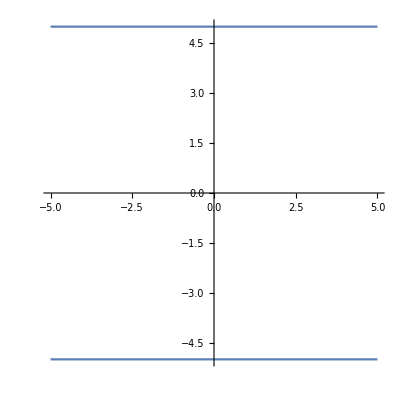

```mathematica
Show[Plot[left[x], {x, -5, 5}, PlotRange->{-5,5}, AspectRatio->1],
Plot[top[x], {x, -5, 5}], Plot[right[x], {x, -5, 5}], Plot[down[x], {x, -5, 5}],
ListPlot[rightDownPoints], ListPlot[rightHighPoints], ListPlot[leftDownPoints], ListPlot[leftHighPoints]]
```

XOR

## Implémentation des tests

Test du Perceptron Linéaire simple

## Cas de test : Simple Linéairement Séparable

### Classification

```mathematica
Clear[model, X, Y, Xtest, Xtest2, Y, Ytest]
```

```mathematica
model = createLinearModel[2,1];
```

NET::netexcptn: A .NET exception occurred: System.EntryPointNotFoundException: Impossible de trouver le point d'entrée 'createLinearModel' dans la DLL 'D:\git\projet_annuel_ibd3a\C++_lib\Dll-Machine-Learning\x64\Debug\Dll-Machine-Learning.dll'.
   à Wolfram.NETLink.DynamicDLLNamespace.DLLWrapper38.createLinearModel(Int32 , Int32 ).

```mathematica
X=Flatten[{positivePointsL, negativePointsL}];
Y = {1,1,1, -1,-1,-1};
```

```mathematica
Xtest = {X[[1]], X[[2]]};
Ytest = {Y[[1]]};
```

```mathematica
linearFitClassificationRosenblatt[model, X, 12 Y, 1, 1000, 0.1];
```

NET::methodargs: Improper arguments supplied for method named linearFitClassificationRosenblatt.

```mathematica
linearClassify[model, Xtest, 2, Ytest, 1];
```

NET::methodargs: Improper arguments supplied for method named linearClassify.

```mathematica
Xtest2 = Partition[Flatten[Table[{i,j},{i, -5, 5, 0.2}, {j, -5, 5, 0.2}]], 2];
```

```mathematica
positive = Select[Xtest2,linearClassify[model, #,2, Ytest,1 ]== 1&];
negative =Select[Xtest2,linearClassify[model, #,2, Ytest,1 ]== -1&];
```

NET::methodargs: Improper arguments supplied for method named linearClassify.

General::stop: Further output of NET::methodargs will be suppressed during this calculation.

NET::methodargs: Improper arguments supplied for method named linearClassify.

General::stop: Further output of NET::methodargs will be suppressed during this calculation.

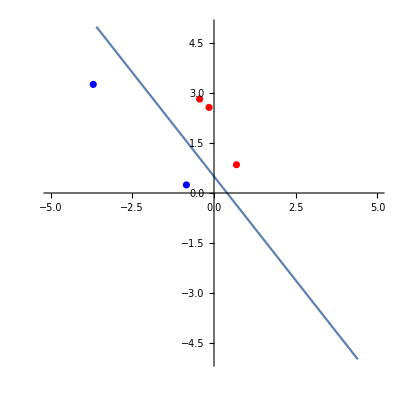

```mathematica
Show[Plot[f[x], {x,-5, 5}, PlotRange->{-5,5},
AspectRatio->1],ListPlot[positive, PlotStyle->Red], ListPlot[negative, PlotStyle->Blue], ListPlot[negativePointsL, PlotStyle->Blue, PlotStyle->Thick],
ListPlot[positivePointsL, PlotStyle->Red, PlotStyle->Thick]]
```

```mathematica
Clear[model, X, Y, Xtest, Xtest2, Y, Ytest];
```

```mathematica
managedTab = NETNew["int[]", 5]
LoadNETType["System.Runtime.InteropServices.Marshal"]
Marshal`Copy[funct, managedTab, 0, 5]
managedTab@GetValue[2]
```

«NETObject[System.Int32[]]»

NETType[System.Runtime.InteropServices.Marshal,68]

NET::methodargs: Improper arguments supplied for method named Copy.

$Failed

0

```mathematica
copyFromNetArray[array_] := Table[array@GetValue[i], {i, 0, array@Length-1}]
```

```mathematica
NETObjectToExpression[managedTab]
```

{0,0,0,0,0}

### Régression

## Cas de test : Simple Non-Linéairement Séparable

### Classification

### Régression

## Cas de test : Cross

## Cas de test : XOR

Test du Perceptron Multi Couches

## Cas de test : Simple Linéairement Séparable

### Classification

```mathematica
Clear[model, X, Y, Xtest, Xtest2, Y, Ytest]
```

```mathematica
structure={2,2,1};
nbLayer=3;
```

```mathematica
model = createMlp[structure,nbLayer];
```

NET::netexcptn: A .NET exception occurred: System.EntryPointNotFoundException: Impossible de trouver le point d'entrée 'createLinearModel' dans la DLL 'D:\git\projet_annuel_ibd3a\C++_lib\Dll-Machine-Learning\x64\Debug\Dll-Machine-Learning.dll'.
   à Wolfram.NETLink.DynamicDLLNamespace.DLLWrapper38.createLinearModel(Int32 , Int32 ).

```mathematica
fitClassification[model, simpleLinearLearningSetX, simpleLinearLearningSetNbData,simpleLinearLearningSetY]
```

```mathematica
(* FOR each data in simpleLinearTestX *)
```

```mathematica
mlpClassify(simpleLinearTestSetX)
```

```mathematica
Plot Resultats
```

## Cas de test : Simple Non-Linéairement Séparable

### Classification

```mathematica
Clear[model, X, Y, Xtest, Xtest2, Y, Ytest]
```

```mathematica
structure={2,2,1};
nbLayer=3;
```

```mathematica
model = createMlp[structure,nbLayer];
```

NET::netexcptn: A .NET exception occurred: System.EntryPointNotFoundException: Impossible de trouver le point d'entrée 'createLinearModel' dans la DLL 'D:\git\projet_annuel_ibd3a\C++_lib\Dll-Machine-Learning\x64\Debug\Dll-Machine-Learning.dll'.
   à Wolfram.NETLink.DynamicDLLNamespace.DLLWrapper38.createLinearModel(Int32 , Int32 ).

```mathematica
fitClassification[model, simpleNonLinearTLearningSetX, simpleNonLinearLearningSetNbData,simpleNonLinearLearningSetY]
```

```mathematica
(* FOR each data in simpleLinearTestX *)
```

```mathematica
mlpClassify(simpleNonLinearTestSetX)
```

```mathematica
Plot Resultats
```

## Cas de test : Cross

### Classification

```mathematica
Clear[model, X, Y, Xtest, Xtest2, Y, Ytest]
```

```mathematica
structure={2,2,1};
nbLayer=3;
```

```mathematica
model = createMlp[structure,nbLayer];
```

NET::netexcptn: A .NET exception occurred: System.EntryPointNotFoundException: Impossible de trouver le point d'entrée 'createLinearModel' dans la DLL 'D:\git\projet_annuel_ibd3a\C++_lib\Dll-Machine-Learning\x64\Debug\Dll-Machine-Learning.dll'.
   à Wolfram.NETLink.DynamicDLLNamespace.DLLWrapper38.createLinearModel(Int32 , Int32 ).

```mathematica
fitClassification[model, crossTestDataSetX, crossTestDataSetNbData,crossTestDataSetY]
```

```mathematica
(* FOR each data in simpleLinearTestX *)
```

```mathematica
mlpClassify(crossTestX)
```

```mathematica
Plot Resultats
```

## Cas de test : XOR

### Classification

```mathematica
Clear[model, X, Y, Xtest, Xtest2, Y, Ytest]
```

```mathematica
structure={2,2,1};
nbLayer=3;
```

```mathematica
model = createMlp[structure,nbLayer];
```

NET::netexcptn: A .NET exception occurred: System.EntryPointNotFoundException: Impossible de trouver le point d'entrée 'createLinearModel' dans la DLL 'D:\git\projet_annuel_ibd3a\C++_lib\Dll-Machine-Learning\x64\Debug\Dll-Machine-Learning.dll'.
   à Wolfram.NETLink.DynamicDLLNamespace.DLLWrapper38.createLinearModel(Int32 , Int32 ).

```mathematica
fitClassification[model, xorTestDataSetX, xorTestDataSetNbData,xorTestDataSetY]
```

```mathematica
(* FOR each data in simpleLinearTestX *)
```

```mathematica
mlpClassify(xorTestX)
```

```mathematica
Plot Resultats
```

Test du RBF

## Cas de test : Simple Linéairement Séparable

```mathematica
Clear[model, X, Y, Xtest, Xtest2, Y, Ytest]
```

```mathematica
model = createLinearModel[2,1];
```

NET::netexcptn: A .NET exception occurred: System.EntryPointNotFoundException: Impossible de trouver le point d'entrée 'createLinearModel' dans la DLL 'D:\git\projet_annuel_ibd3a\C++_lib\Dll-Machine-Learning\x64\Debug\Dll-Machine-Learning.dll'.
   à Wolfram.NETLink.DynamicDLLNamespace.DLLWrapper38.createLinearModel(Int32 , Int32 ).

```mathematica
X=Flatten[{positivePointsL, negativePointsL}];
Y = {1,1,1, -1,-1,-1};
```

```mathematica
Xtest = {X[[1]], X[[2]]};
Ytest = {Y[[1]]};
```

```mathematica
linearFitClassificationRosenblatt[model, X, 12 Y, 1, 1000, 0.1];
```

NET::methodargs: Improper arguments supplied for method named linearFitClassificationRosenblatt.

```mathematica
linearClassify[model, Xtest, 2, Ytest, 1];
```

NET::methodargs: Improper arguments supplied for method named linearClassify.

```mathematica
Xtest2 = Partition[Flatten[Table[{i,j},{i, -5, 5, 0.2}, {j, -5, 5, 0.2}]], 2];
```

```mathematica
positive = Select[Xtest2,linearClassify[model, #,2, Ytest,1 ]== 1&];
negative =Select[Xtest2,linearClassify[model, #,2, Ytest,1 ]== -1&];
```

NET::methodargs: Improper arguments supplied for method named linearClassify.

General::stop: Further output of NET::methodargs will be suppressed during this calculation.

NET::methodargs: Improper arguments supplied for method named linearClassify.

General::stop: Further output of NET::methodargs will be suppressed during this calculation.

```mathematica
Show[Plot[f[x], {x,-5, 5}, PlotRange->{-5,5},
AspectRatio->1],ListPlot[positive, PlotStyle->Red], ListPlot[negative, PlotStyle->Blue], ListPlot[negativePointsL, PlotStyle->Blue, PlotStyle->Thick],
ListPlot[positivePointsL, PlotStyle->Red, PlotStyle->Thick]]
```

-Graphics-

```mathematica
Clear[model, X, Y, Xtest, Xtest2, Y, Ytest];
```

```mathematica
managedTab = NETNew["int[]", 5]
LoadNETType["System.Runtime.InteropServices.Marshal"]
Marshal`Copy[funct, managedTab, 0, 5]
managedTab@GetValue[2]
```

«NETObject[System.Int32[]]»

NETType[System.Runtime.InteropServices.Marshal,68]

NET::methodargs: Improper arguments supplied for method named Copy.

$Failed

0

```mathematica
copyFromNetArray[array_] := Table[array@GetValue[i], {i, 0, array@Length-1}]
```

```mathematica
NETObjectToExpression[managedTab]
```

{0,0,0,0,0}

## Cas de test : Simple Non-Linéairement Séparable

## Cas de test : Cross

## Cas de test : XOR